```mathematica
twoddata=data⟦All,;;2⟧;
```

```mathematica
data=Table[QuantityMagnitude/@AstronomicalData["Mercury",{"Position",i}],{i,DateRange[{2015,1,1},{2016,1,1}]}]/10^10;
```

```mathematica
Manipulate[Graphics[{Circle[{0,0},r],Point[twoddata],Point[{0,0}]}],{r,0,10}]
```

```mathematica
sol=x[t]/.NDSolve[{x''[t]==(-2 x[t])/Norm[x[t]]^3,x[0]=={1,0},x'[0]=={0,1}},x[t],{t,0,100}]⟦1⟧
```

InterpolatingFunction[{{0., 100.}}, <>][t]

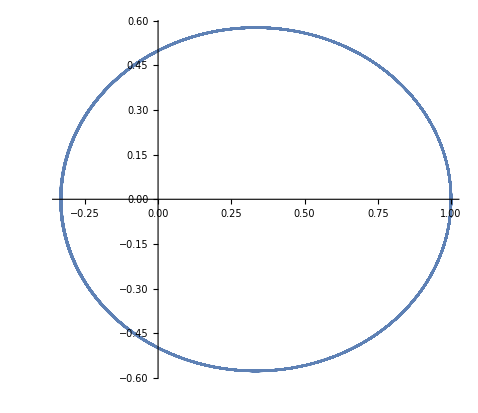

```mathematica
ParametricPlot[sol,{t,0,100}]
```

```mathematica
Manipulate[Module[{xo={a,0},u0={0,2.37},sol},sol=x[t]/.NDSolve[{x''[t]==(-g x[t])/Norm[x[t]]^3,x[0]==xo,x'[0]==u0},x[t],{t,0,100}]⟦1⟧;ParametricPlot[sol,{t,0,100},PlotRange->3]],{g,3,10},{a,1,5}]
```

```mathematica
Graphics3D[Point[data]]
```

-Graphics3D-

```mathematica
Quantity[-2.657094542468515*^10, "Meters"]
```

-2.65709×10^10 m

```mathematica
QuantityMagnitude[Quantity[-2.657094542468515*^10,"Meters"]]
```

-2.65709×10^10